```mathematica
given Potential, find the Field Line
```

## Calling nesccery function

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Cartesian[x,y,z]]
```

Cartesian[x,y,z]

```mathematica
Needs["VectorFieldPlots`"]
```

# 2 - D potential

## Given Condition of potential

```mathematica
u[x,y] (* u  satisfly Laplacian equation *)
i.e. ∇^2 u=(∂^2 u)/(∂x^2)+(∂^2 u)/(∂y^2)=0
```

```mathematica
v[x,y]=∫((∂ v)/(∂x)ⅆx+(∂ v)/(∂y)ⅆy)=-∫(∂ u)/(∂y)ⅆx+∫(∂ u)/(∂x)ⅆy
```

```mathematica
(* Orthogonal of the field*)
∇u[x,y].∇v[x,y]==0
```

```mathematica
(* by Cauchy-reiman equation *)
```

```mathematica
(∂u)/(∂x)=(∂v)/(∂y)
(∂u)/(∂y)=-(∂v)/(∂x)
```

```mathematica
∇u[x,y].∇v[x,y]==0
((∂u)/(∂x),(∂u)/(∂y)).(-(∂u)/(∂y),(∂u)/(∂x))=0
-(∂u)/(∂x)(∂u)/(∂y)+(∂u)/(∂y)(∂u)/(∂x)=0
```

## Derviation of v From Cauchy-Riemann Relation

```mathematica
(∂v)/(∂x)=-(∂u)/(∂y)
(∂v)/(∂y)=(∂u)/(∂x)
```

```mathematica
∫(∂v)/(∂x)ⅆx=-∫(∂u)/(∂y)ⅆx
v[x,y]=-∫(∂u)/(∂y)ⅆx+f[y]
(∂v[x,y])/(∂y)=-∫(∂^2 u)/(∂y^2)ⅆx+ⅆf[y]/ⅆy
ⅆf[y]/ⅆy=∫(∂^2 u)/(∂y^2)ⅆx+(∂u)/(∂x)
f[y]=∫(∫(∂^2 u)/(∂y^2)ⅆx)ⅆy+∫(∂u)/(∂x)ⅆy= Const.+∫(∂u)/(∂x)ⅆy
```

```mathematica
Therefore: v[x,y]=-∫(∂u)/(∂y)ⅆx+∫(∂u)/(∂x)ⅆy+Constant
```

```mathematica
∫(∂v)/(∂y)ⅆy=∫(∂u)/(∂x)ⅆy
v[x,y]=∫(∂u)/(∂x)ⅆy+g[x]
(∂v[x,y])/(∂x)=∫(∂^2 u)/(∂x^2)ⅆy+ⅆg[x]/ⅆx
ⅆg[x]/ⅆx=-∫(∂^2 u)/(∂x^2)ⅆy-(∂u)/(∂y)
g[x]=-∫(∫(∂^2 u)/(∂x^2)ⅆy)ⅆx-∫(∂u)/(∂y)ⅆx=Const.-∫(∂u)/(∂y)ⅆx
```

```mathematica
Therefore: v[x,y]=-∫(∂u)/(∂y)ⅆx+∫(∂u)/(∂x)ⅆy+Const.
```

```mathematica
Therefore: v[x,y]=-∫(∂u)/(∂y)ⅆx+∫(∂u)/(∂x)ⅆy +Const.(* DONE *)
```

```mathematica
(* Case for non Zero Laplacian u (source) *)
???
```

## Example

```mathematica
u[x_,y_] :=Exp[x]Sin[y]
```

```mathematica
Laplacian[u[x,y]] (*checking Laplacian*)
```

0

```mathematica
(*Calculate v*)
v=∫Derivative[0,1][u][x,y]ⅆx-∫Derivative[1,0][u][x,y]ⅆy
```

2 ⅇ^x Cos[y]

```mathematica
(* Checking Orthogonal*)
Grad[u[x,y]].Grad[v]
```

0

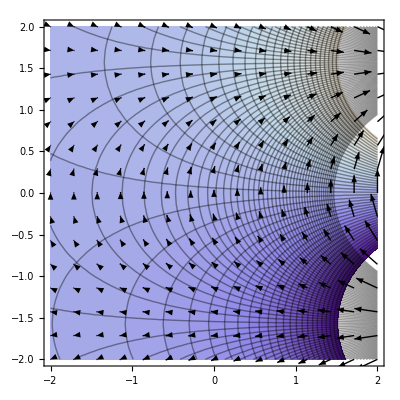

```mathematica
(* Display Contour of u and v *)
Show[
ContourPlot[u[x,y],{x,-2,2},{y,-2,2},Contours->Function[{min,max},Range[min,max,0.2]]],
ContourPlot[v,{x,-2,2},{y,-2,2},Contours->Function[{min,max},Range[min,max,0.2]],ContourShading->None],
GradientFieldPlot[u[x,y], {x, -2, 2}, {y, -2, 2}]
]
```

```mathematica
******************************************
```

```mathematica
3-D
```

```mathematica
u[x,y,z]
```

```mathematica
Grad[u[x,y,z]]
```

{u^(1,0,0)[x,y,z],u^(0,1,0)[x,y,z],u^(0,0,1)[x,y,z]}

```mathematica
((∂u)/(∂x),(∂u)/(∂y),(∂u)/(∂z))
```

```mathematica
Guess
```

```mathematica
(∂v)/(∂x)=(∂u)/(∂y)-(∂u)/(∂z)
```

```mathematica
(∂v)/(∂y)=(∂u)/(∂z)-(∂u)/(∂x)
```

```mathematica
(∂v)/(∂z)=(∂u)/(∂x)-(∂u)/(∂y)
```

```mathematica
*****************????
```

```mathematica
v[x,y,z]=∫(∂u)/(∂y)-(∂u)/(∂z)ⅆx+∫(∂u)/(∂z)-(∂u)/(∂x)ⅆy+∫(∂u)/(∂x)-(∂u)/(∂y)ⅆz
```

```mathematica
**************
```

```mathematica
v[x,y,z]=∫((∂u)/(∂y)-(∂u)/(∂z))ⅆx+f[y,z]
(∂v)/(∂y)=∫((∂^2 u)/(∂y^2)-(∂^2 u)/(∂y∂z))ⅆx+(∂ f[y,z])/(∂y)=(∂u)/(∂z)-(∂u)/(∂x)
```

```mathematica
(∂ f[y,z])/(∂y)=(∂u)/(∂z)-(∂u)/(∂x)-∫((∂^2 u)/(∂y^2)-(∂^2 u)/(∂y∂z))ⅆx
```

```mathematica
f[y,z]=∫((∂u)/(∂z)-(∂u)/(∂x))ⅆy-∫∫((∂^2 u)/(∂y^2)-(∂^2 u)/(∂y∂z))ⅆxⅆy+g[z]
```

```mathematica
// f[y,z]=∫((∂u)/(∂z)-(∂u)/(∂x))ⅆy-∫((∂u)/(∂y)-(∂u)/(∂z))ⅆx+g[z]
```

```mathematica
//v[x,y,z]=∫((∂u)/(∂z)-(∂u)/(∂x))ⅆy+g[z]
```

```mathematica
(∂v)/(∂z)=(∂u)/(∂x)-(∂u)/(∂y)=∫((∂^2 u)/(∂z∂y)-(∂^2 u)/(∂z^2))ⅆx+∫((∂^2 u)/(∂z^2)-(∂^2 u)/(∂z∂x))ⅆy-∫∫((∂^3 u)/(∂y^2∂z)-(∂^3 u)/(∂y∂z^2))ⅆxⅆy+(∂g[z])/(∂z)
```

```mathematica
// (∂v)/(∂z)=(∂u)/(∂x)-(∂u)/(∂y)=∫((∂^2 u)/(∂z^2)-(∂^2 u)/(∂z∂x))ⅆy+(∂g[z])/(∂z)
```

```mathematica
(∂g[z])/(∂z)=-∫((∂^2 u)/(∂z∂y)-(∂^2 u)/(∂z^2))ⅆx-∫((∂^2 u)/(∂z^2)-(∂^2 u)/(∂z∂x))ⅆy+∫(∫((∂^3 u)/(∂y^2∂z)-(∂^3 u)/(∂y∂z^2))ⅆx)ⅆy+((∂u)/(∂x)-(∂u)/(∂y))
```

```mathematica
//(∂g[z])/(∂z)=-∫((∂^2 u)/(∂z^2)-(∂^2 u)/(∂z∂x))ⅆy+((∂u)/(∂x)-(∂u)/(∂y))
```

```mathematica
g[z]=-∫∫(∂^2 u)/(∂z∂y)-(∂^2 u)/(∂z^2)ⅆxⅆz-∫∫(∂^2 u)/(∂z^2)-(∂^2 u)/(∂z∂x)ⅆyⅆz+∫∫∫((∂^3 u)/(∂y^2∂z)-(∂^3 u)/(∂y∂z^2))ⅆxⅆyⅆz+∫((∂u)/(∂x)-(∂u)/(∂y))ⅆz
```

```mathematica
//g[z]=-∫((∂u)/(∂z)-(∂u)/(∂x))ⅆy+∫((∂u)/(∂x)-(∂u)/(∂y))ⅆz
```

```mathematica
// v[x,y,z]=∫((∂u)/(∂x)-(∂u)/(∂y))ⅆz
```

```mathematica
v[x,y,z]=∫((∂u)/(∂y)-(∂u)/(∂z))ⅆx+∫((∂u)/(∂z)-(∂u)/(∂x))ⅆy+∫((∂u)/(∂x)-(∂u)/(∂y))ⅆz-∫∫((∂^2 u)/(∂y^2)-(∂^2 u)/(∂y∂z))ⅆxⅆy-∫∫((∂^2 u)/(∂z^2)-(∂^2 u)/(∂z∂x))ⅆyⅆz-∫∫((∂^2 u)/(∂z∂y)-(∂^2 u)/(∂z^2))ⅆxⅆz+∫∫∫((∂^3 u)/(∂y^2∂z)-(∂^3 u)/(∂y∂z^2))ⅆxⅆyⅆz
```

```mathematica
Integrate[(D[u[x,y,z],y]-D[u[x,y,z],z]),x]+
Integrate[(D[u[x,y,z],z]-D[u[x,y,z],x]),y]+
Integrate[(D[u[x,y,z],x]-D[u[x,y,z],y]),z]-
Integrate[(D[u[x,y,z],{y,2}]-D[u[x,y,z],z,y]),x,y]-
Integrate[(D[u[x,y,z],z,y]-D[u[x,y,z],{z,2}]),x,z]-
Integrate[(D[u[x,y,z],{z,2}]-D[u[x,y,z],z,x]),y,z]+
Integrate[(D[u[x,y,z],{y,2},z]-D[u[x,y,z],y,{z,2}]),x,y,z]
```

-x^2/2+x y-y^2/2+z^2

```mathematica
// Special case u[x,y,z]=u[x,y],
i.e. ((∂u)/(∂z))=0
```

```mathematica
(∂v)/(∂x)=(∂u)/(∂y)-(∂u)/(∂z)
```

```mathematica
(∂v)/(∂y)=(∂u)/(∂z)-(∂u)/(∂x)
```

```mathematica
(∂v)/(∂z)=(∂u)/(∂x)-(∂u)/(∂y)
```

```mathematica
-> (∂v)/(∂x)=(∂u)/(∂y),(∂v)/(∂y)=-(∂u)/(∂x),(∂v)/(∂z)=0 ??
```

```mathematica
v[x,y]=∫((∂u)/(∂y))ⅆx+∫(-(∂u)/(∂x))ⅆy-∫∫(∂^2 u)/(∂y^2)ⅆxⅆy
v[x,y]=∫((∂u)/(∂y))ⅆx+∫(-(∂u)/(∂x))ⅆy+∫∫(∂^2 u)/(∂x^2)ⅆxⅆy
```

```mathematica
v[x,y]=∫((∂u)/(∂y))ⅆx+∫(-(∂u)/(∂x))ⅆy+∫(∂u)/(∂x)ⅆy
```

```mathematica
v[x,y]=∫((∂u)/(∂y))ⅆx+∫(-(∂u)/(∂x))ⅆy-∫(∂v)/(∂y)ⅆy
```

```mathematica
v[x,y]=1/2(∫((∂u)/(∂y))ⅆx-∫(∂u)/(∂x)ⅆy) !!! oh yes!
```

```mathematica
******************************************************
```

```mathematica
u[x,y,z]:=x z - y z
```

```mathematica
Laplacian[u[x,y,z], Cartesian]
```

0

```mathematica
Integrate[(D[u[x,y,z],y]-D[u[x,y,z],z]),x]+
Integrate[(D[u[x,y,z],z]-D[u[x,y,z],x]),y]+
Integrate[(D[u[x,y,z],x]-D[u[x,y,z],y]),z]
```

-x^2/2+2 x y-y^2/2-x z-y z+z^2

```mathematica
Laplacian[-x^2/2+2 x y-y^2/2-x z-y z+z^2]
```

0

```mathematica
Simplify[Grad[u[x,y,z]].Grad[-x^2/2+2 x y-y^2/2-x z-y z+z^2]]
```

-(x-y) (x+y+z)

```mathematica
x z - y z/.z->1
```

x-y

```mathematica
-x^2/2+x y-y^2/2+z^2/.z->1
```

1-x^2/2+x y-y^2/2

```mathematica
ContourPlot3D[x z - y z,{x,-2,2},{y,-2,2},{z,-2,2}, Contours->20]
```

-Graphics3D-

```mathematica
Show[
ContourPlot3D[x z - y z,{x,-2,2},{y,-2,2},{z,-2,2}],
GradientFieldPlot3D[(x z - y z),{x,-2,2},{y,-2,2},{z,-2,2},VectorHeads->True]
]
```

-Graphics3D-

-Graphics3D-

```mathematica
*********************************
```

```mathematica
u[x_,y_,z_]:= x y z
```

```mathematica
Laplacian[u[x,y,z], Cartesian]
```

0

```mathematica
Integrate[(D[u[x,y,z],y]-D[u[x,y,z],z]),x]+
Integrate[(D[u[x,y,z],z]-D[u[x,y,z],x]),y]+
Integrate[(D[u[x,y,z],x]-D[u[x,y,z],y]),z]-
Integrate[(D[u[x,y,z],{y,2}]-D[u[x,y,z],z,y]),x,y]-
Integrate[(D[u[x,y,z],z,y]-D[u[x,y,z],{z,2}]),x,z]-
Integrate[(D[u[x,y,z],{z,2}]-D[u[x,y,z],z,x]),y,z]+
Integrate[(D[u[x,y,z],{y,2},z]-D[u[x,y,z],y,{z,2}]),x,y,z]
```

(x y^2)/2-(x z^2)/2+(y z^2)/2

```mathematica
Laplacian[(x y^2)/2-(x z^2)/2+(y z^2)/2]
```

y

```mathematica
ContourPlot3D[x y z,{x,-2,2},{y,-2,2},{z,-2,2}, Contours->20]
```

-Graphics3D-

```mathematica
Show[
ContourPlot3D[x y z,{x,-2,2},{y,-2,2},{z,-2,2}],
GradientFieldPlot3D[x y z,{x,-2,2},{y,-2,2},{z,-2,2},VectorHeads->True]
]
```

-Graphics3D-

```mathematica
ContourPlot3D[(x y^2)/2-(x z^2)/2+(y z^2)/2,{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

```mathematica
(∂v)/(∂x)=a
(∂v)/(∂y)=b
(∂v)/(∂z)=c
```

```mathematica
v[x,y,z]=∫aⅆx+f[y,z]
```

```mathematica
(∂v)/(∂y)=b=∫(∂a)/(∂y)ⅆx+(∂f[y,z])/(∂y)
```

```mathematica
(∂f[y,z])/(∂y)=b-∫(∂a)/(∂y)ⅆx
```

```mathematica
f[y,z]=∫bⅆy-∫(∫(∂a)/(∂y)ⅆx)ⅆy+g[z]
```

```mathematica
v[x,y,z]=∫aⅆx+∫bⅆy-∫∫(∂a)/(∂y)ⅆxⅆy+g[z]
```

```mathematica
c=∫(∂a)/(∂z)ⅆx+∫(∂b)/(∂z)ⅆy-∫∫(∂^2 a)/(∂z∂y)ⅆxⅆy+(∂g[z])/(∂z)
```

```mathematica
(∂g[z])/(∂z)=c-∫(∂a)/(∂z)ⅆx-∫(∂b)/(∂z)ⅆy+∫∫(∂^2 a)/(∂z∂y)ⅆxⅆy
```

```mathematica
g[z]=∫cⅆz-∫∫(∂a)/(∂z)ⅆxⅆz-∫∫(∂b)/(∂z)ⅆyⅆz+∫∫∫(∂^2 a)/(∂z∂y)ⅆxⅆyⅆz
```

```mathematica
v[x,y,z]=∫aⅆx+∫bⅆy+∫cⅆz-∫∫(∂a)/(∂y)ⅆxⅆy-∫∫(∂a)/(∂z)ⅆxⅆz-∫∫(∂b)/(∂z)ⅆyⅆz+∫∫∫(∂^2 a)/(∂z∂y)ⅆxⅆyⅆz
```

```mathematica
how about
```

```mathematica
v[x,y,z]=∫aⅆx+∫bⅆy+∫cⅆz-∫∫(∂c)/(∂z)ⅆxⅆy-∫∫(∂b)/(∂y)ⅆxⅆz-∫∫(∂c)/(∂x)ⅆyⅆz+∫∫∫((∂^2 a)/(∂z∂y)+(∂^2 b)/(∂x∂z)+(∂^2 c)/(∂x∂y))ⅆxⅆyⅆz
```

```mathematica
for c=0
v[x,y]=∫aⅆx+∫bⅆy-∫∫(∂b)/(∂y)ⅆxⅆz
```

```mathematica
well~
```

```mathematica
Plot3D[x+y
```